## Clear

```mathematica
Clear["Global`*"]
```

## Matrix Definition

```mathematica
v={1,2,-1};
```

```mathematica
z=2v;
```

```mathematica
m={v,z}
```

{{1,2,-1},{2,4,-2}}

```mathematica
MatrixForm[m]
```

(1 | 2 | -1
2 | 4 | -2)

## Define List

```mathematica
data=Table[{x,x^4},{x,-3,3,.2}]
```

{{-3.,81.},{-2.8,61.4656},{-2.6,45.6976},{-2.4,33.1776},{-2.2,23.4256},{-2.,16.},{-1.8,10.4976},{-1.6,6.5536},{-1.4,3.8416},{-1.2,2.0736},{-1.,1.},{-0.8,0.4096},{-0.6,0.1296},{-0.4,0.0256},{-0.2,0.0016},{0.,0.},{0.2,0.0016},{0.4,0.0256},{0.6,0.1296},{0.8,0.4096},{1.,1.},{1.2,2.0736},{1.4,3.8416},{1.6,6.5536},{1.8,10.4976},{2.,16.},{2.2,23.4256},{2.4,33.1776},{2.6,45.6976},{2.8,61.4656},{3.,81.}}

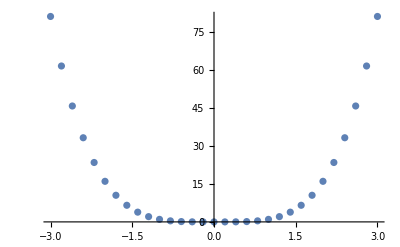

```mathematica
ListPlot[data]
```

```mathematica
data2=Table[{x,x},{x,-3,3,.2}];
```

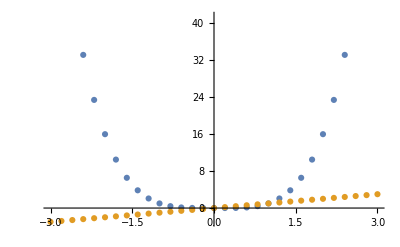

```mathematica
ListPlot[{data,data2}]
```

## Solve Equation

```mathematica
Solve[{x^2+y-2==0,x-3y==4},{x,y}]
```

{{x→-2,y→-2},{x→5/3,y→-7/9}}

```mathematica
{x,y}/.Solve[{x^2+y-2==0,x-3y==4},{x,y}]
```

{{-2,-2},{5/3,-7/9}}

## If I cannot solve?

```mathematica
Clear["Global`*"]
```

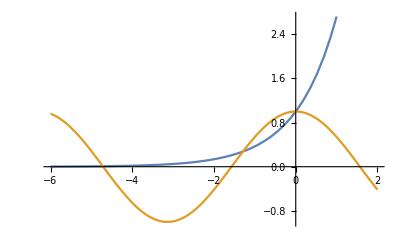

```mathematica
Plot[{Exp[x],Cos[x]},{x,-6,2}]
```

```mathematica
FindRoot[Exp[x]-Cos[x]==0,{x,-1.5}]
```

{x→-1.2927}

```mathematica
x/.%
```

-1.2927

## Iteration is also good

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]= Exp[x]-Cos[x];
```

```mathematica
newton[x00_]:=Module[{ϵ,x0,Δx,x},ϵ=10^-8;x0=x00;x=x0+1;Δx=x-x0;While[Abs[Δx]>ϵ,x=x0-f[x0]/f'[x0];Δx=x-x0;
x0=x];
x]
```

```mathematica
newton[-1.5]
```

-1.2927

## ContourPlot

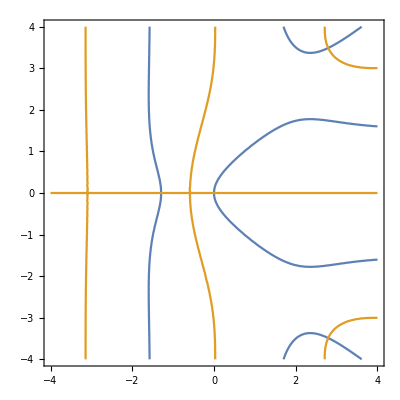

```mathematica
ContourPlot[{Re[f[x+I y]]==0,Im[f[x+I y]]==0},{x,-4,4},{y,-4,4}]
```

## Draw Vector Fields

### 1st order ODE

```mathematica
f[t_,v_]= t - v;
```

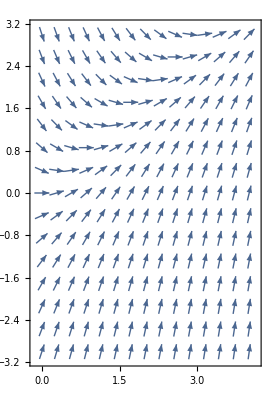

```mathematica
VectorPlot[{1,f[t,v]},{t,0,4},{v,-3,3},VectorScale->{0.04,.5,None},AspectRatio->Automatic]
```

### 2nd order ODE

```mathematica
f[x_,v_] = -x-v/2;
```

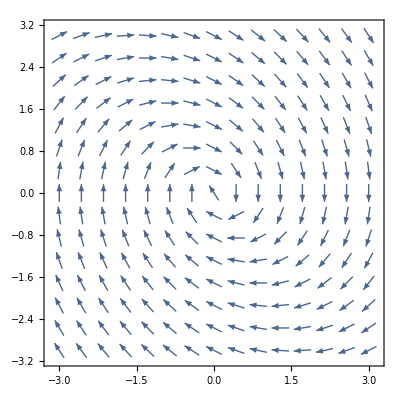

```mathematica
VectorPlot[{v,f[x,v]},{x,-3,3},{v,-3,3},VectorScale->{0.04,.5,None},AspectRatio->Automatic]
```

## Solve Differential Eqn

### Without Initial Value

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[m x''[t]==-k x[t],x[t],t]
```

{{x[t]→C[1] Cos[(√k t)/(√m)]+C[2] Sin[(√k t)/(√m)]}}

```mathematica
xs[t_]= x[t]/.%[[1]]
```

C[1] Cos[(√k t)/(√m)]+C[2] Sin[(√k t)/(√m)]

### With Initial Value

```mathematica
Clear[x]
```

```mathematica
DSolve[{m x''[t]==-k x[t],x[0]==x0,x'[0]==v0},x[t],t]
```

{{x[t]→(√k x0 Cos[(√k t)/(√m)]+√m v0 Sin[(√k t)/(√m)])/(√k)}}

### Solve System of Eqns

```mathematica
DSolve[{x'[t]==v[t],m v'[t]==-k x[t],x[0]==x0,v[0]==v0},{x[t],v[t]},t]
```

{{v[t]→(√m v0 Cos[(√k t)/(√m)]-√k x0 Sin[(√k t)/(√m)])/(√m),x[t]→(√k x0 Cos[(√k t)/(√m)]+√m v0 Sin[(√k t)/(√m)])/(√k)}}

## Solve ODE numerically

```mathematica
NDSolve[{x'[t]==t/(x[t]+t)^2,x[0]==1},x,{t,0,4}]
```

{{x→InterpolatingFunction[{{0., 4.}}, <>]}}

```mathematica
xs[t_]= x[t]/.%[[1]]
```

InterpolatingFunction[{{0., 4.}}, <>][t]

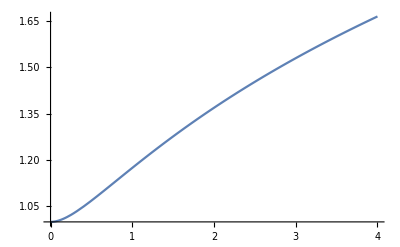

```mathematica
Plot[xs[t],{t,0,4}]
```

## Euler’s Method (1st Order ODE)

```mathematica
Clear[xs]
```

```mathematica
f[t_,v_]= -v+t;
```

```mathematica
euler[Δt_,v0_,tt_]:= Module[{v,t,tsol},t[n_]= n Δt;
v[n_]:=v[n]= v[n-1]+ Δt f[t[n-1],v[n-1]];
v[0]=v0;
tsol=Table[{t[n],v[n]},{n,0,tt/Δt+1}];
xs=Interpolation[tsol]]
```

```mathematica
euler[.1,0,5.]
```

InterpolatingFunction[{{0., 5.1}}, <>]

## Euler’s Method (2nd Order ODE)

```mathematica
Clear["Global`*"]
```

```mathematica
euler[Δt_,z0_,tt_]:= Module[{z,t,tsol},t[n_]= n Δt;
z[n_]:=z[n]= z[n-1]+ Δt F[t[n-1],z[n-1]];
z[0]=z0;
tsol=Table[{t[n],z[n][[1]]},{n,0,tt/Δt+1}];
xs=Interpolation[tsol]]
```

```mathematica
F[t_,z_]:= {v,-x}/.{x->z[[1]],v->z[[2]]}
```

```mathematica
euler[.1,{1,0},4Pi]
```

InterpolatingFunction[{{0., 12.6}}, <>]

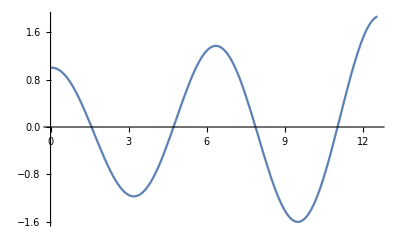

```mathematica
Plot[xs[t],{t,0,4Pi}]
```

## Predictor-Corrector Method (2nd Order ODE)

```mathematica
Clear["Global`*"]
```

```mathematica
PC[Δt_,z0_,tt_]:= Module[{z,t,tsol},t[n_]= n Δt;
zp[n_]:= z[n-1]+ Δt F[t[n-1],z[n-1]];
z[n_]:=z[n]= z[n-1]+ 1/2 Δt (F[t[n-1],z[n-1]]+F[t[n],zp[n]]);
z[0]=z0;
tsol=Table[{t[n],z[n][[1]]},{n,0,tt/Δt+1}];
xs=Interpolation[tsol]]
```

```mathematica
F[t_,z_]:= {v,-x}/.{x->z[[1]],v->z[[2]]}
```

```mathematica
PC[.1,{0,1},5.]
```

InterpolatingFunction[{{0., 5.1}}, <>]

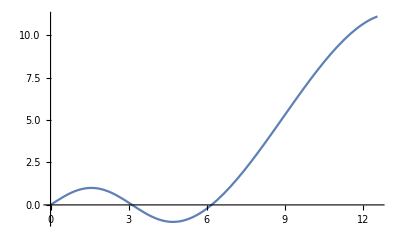

```mathematica
Plot[xs[t],{t,0,4Pi}]
```

### Or use n as variable ( faster )

```mathematica
Clear["Global`*"]
```

```mathematica
f[t_] = t Exp[-3 t];
```

```mathematica
Δt = 0.01; t[n_]= n Δt;
```

```mathematica
F[z_,n_]:= {z[[2]],f[t[n]]-2 z[[2]]};
```

```mathematica
zp[n_]:= z[n-1]+ Δt F[z[n-1],n-1];
```

```mathematica
z[n_]:=z[n]= z[n-1]+ 1/2 Δt (F[z[n-1],n-1]+F[zp[n],n]);
```

```mathematica
z[0]= {0,1};
```

```mathematica
tsol=Table[{t[n],z[n][[1]]},{n,0,300}];
```

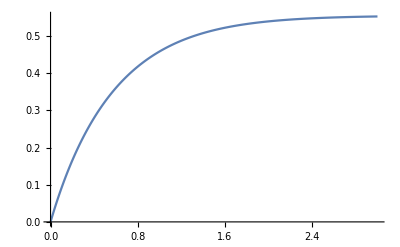

```mathematica
ListPlot[%, Joined -> True]
```

## Shooting Method (BVP)

```mathematica
Clear["Global`*"]
```

```mathematica
T=1;
g=9.8;
c=1;
m=1;
```

```mathematica
h=1.
```

1.

```mathematica
sol[v0_]:= NDSolve[{y''[t]==-g-c/m (y'[t])^2 Sign[y'[t]],y[0]==0,y'[0]==v0},y,{t,0,T}]
```

```mathematica
sol[1.]
```

{{y→InterpolatingFunction[{{0., 1.}}, <>]}}

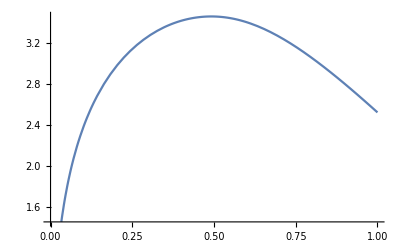

```mathematica
Plot[y[t]/.sol[100.][[1]]//Evaluate,{t,0,T}]
```

```mathematica
yf[v0_]:= (y[T]/.sol[v0][[1]])/; v0∈Reals
```

```mathematica
yf[100.]
```

2.52596

```mathematica
FindRoot[yf[v0]==h,{v0,50}]
```

{v0→23.6648}

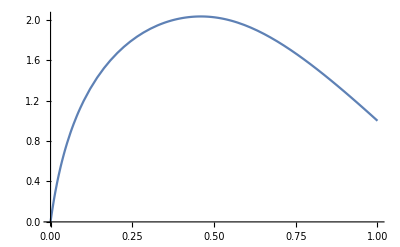

```mathematica
Plot[y[t]/.sol[v0/.%][[1]]//Evaluate,{t,0,T},PlotRange->All]
```

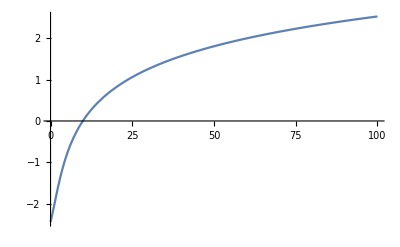

```mathematica
Plot[yf[v0],{v0,0,100}]
```

## System of ODE ( KroneckerDelta)

```mathematica
Clear["Global`*"]
```

```mathematica
L[n_,m_]= KroneckerDelta[n,m]+(-1+u[n-1]Δt)KroneckerDelta[n-1,m]
```

KroneckerDelta[m,n]+KroneckerDelta[m,-1+n] (-1+Δt u[-1+n])

```mathematica
Lmat=Table[L[n,m],{n,0,4},{m,0,4}]
```

{{1,0,0,0,0},{-1+Δt u[0],1,0,0,0},{0,-1+Δt u[1],1,0,0},{0,0,-1+Δt u[2],1,0},{0,0,0,-1+Δt u[3],1}}

```mathematica
MatrixForm[%]
```

(1 | 0 | 0 | 0 | 0
-1+Δt u[0] | 1 | 0 | 0 | 0
0 | -1+Δt u[1] | 1 | 0 | 0
0 | 0 | -1+Δt u[2] | 1 | 0
0 | 0 | 0 | -1+Δt u[3] | 1)

```mathematica
fvec=Table[Δt f[n-1],{n,0,4}]
```

{Δt f[-1],Δt f[0],Δt f[1],Δt f[2],Δt f[3]}

```mathematica
fvec[[1]]=a
```

a

```mathematica
fvec
```

{a,Δt f[0],Δt f[1],Δt f[2],Δt f[3]}

```mathematica
Δt=.1;
u[n_]= n Δt;
a=1;f[n_]= n Δt;
```

```mathematica
Lmat
```

{{1,0,0,0,0},{-1.,1,0,0,0},{0,-0.99,1,0,0},{0,0,-0.98,1,0},{0,0,0,-0.97,1}}

```mathematica
x=Inverse[Lmat].fvec
```

{1.,1.,1.,1.,1.}

## Define PieceWise Function and Fourier Series (Trig)

```mathematica
Clear["Global`*"]
```

```mathematica
T=1;
```

```mathematica
f[t_]= Piecewise[{{2 t/T,0<t<T/2},{2-2t/T,T/2<t<T}}]
```

Piecewise[{{2 t, 0<t<1/2}, {2-2 t, 1/2<t<1}, {0, True}}]

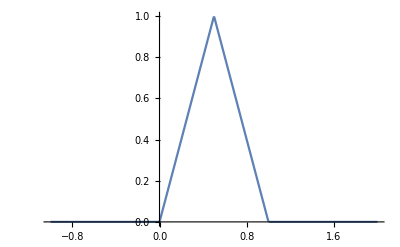

```mathematica
Plot[f[t],{t,-1,2}]
```

```mathematica
f[t_]:= f[t-T]/; t>T
f[t_]:=f[t+T]/; t<0
```

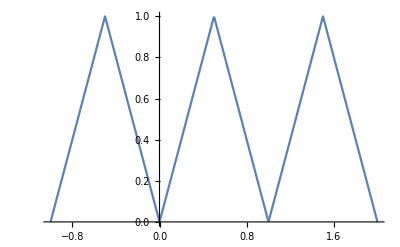

```mathematica
Plot[f[t],{t,-1,2}]
```

```mathematica
a[0]= 1/T Integrate[f[t],{t,0,T}]
```

1/2

```mathematica
a[m_]= 2/T Integrate[f[t] Cos[2 Pi m t/T],{t,0,T}]
```

(-1+2 Cos[m π]-Cos[2 m π])/(m^2 π^2)

```mathematica
b[m_]= 2/T Integrate[f[t]Sin[m 2 Pi t/T],{t,0,T}]
```

(2 Sin[m π]-Sin[2 m π])/(m^2 π^2)

```mathematica
fapprox[t_,M_]:= a[0]+Sum[a[m] Cos[m 2 Pi t/T]+b[m]Sin[m 2 Pi t/T],{m,1,M}]
```

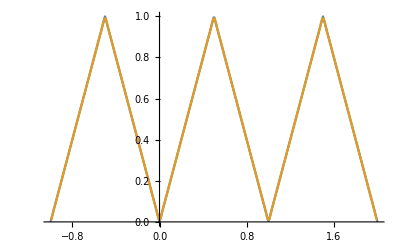

```mathematica
Plot[{f[t],fapprox[t,20]},{t,-1,2}]
```

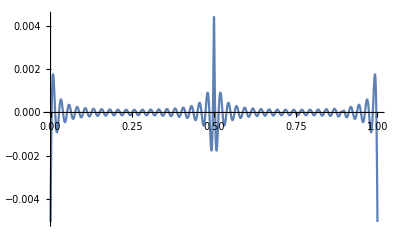

```mathematica
Plot[{f[t]-fapprox[t,40]}//Evaluate,{t,0,1},PlotRange->All]
```

```mathematica
Manipulate[Plot[{f[t]-fapprox[t,M]},{t,-1,1},PlotRange->All],{M,5,20,5}]
```

## Fourier Series (Exponential)

```mathematica
Clear["Global`*"]
```

```mathematica
f[t_] = Piecewise[{{2t/T,0<t<T/2},{2-2t/T,T/2<t<T}}]
```

Piecewise[{{(2 t)/T, 0<t<T/2}, {2-(2 t)/T, T/2<t<T}, {0, True}}]

```mathematica
f[t_]:= f[t-T]/; t>T
f[t_]:= f[t+T]/; t<0
```

```mathematica
T=1;
```

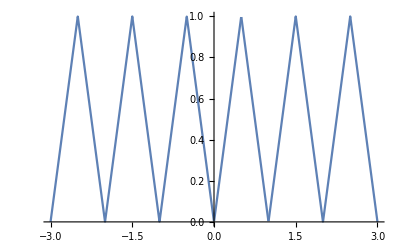

```mathematica
Plot[f[t],{t,-3,3}]
```

```mathematica
c[m_]= Integrate[f[t] Exp[I m 2Pi t/T],{t,0,T}]/T
```

-((-1+ⅇ^(ⅈ m π))^2)/(2 m^2 π^2)

```mathematica
c[0]=Limit[c[m],m->0]
```

1/2

```mathematica
fapprox[t_,M_]:= Sum[c[m] Exp[-I m 2Pi t/T],{m,-M,M}]
```

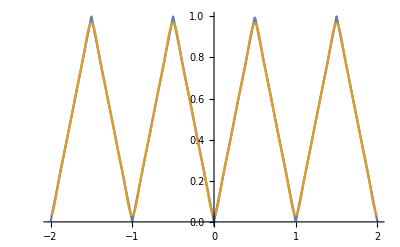

```mathematica
Plot[{f[t],fapprox[t,5]},{t,-2,2}]
```

```mathematica
c[n]
```

-((-1+ⅇ^(ⅈ n π))^2)/(2 n^2 π^2)

```mathematica
Table[c[n],{n,0,5}]
```

{1/2,-2/π^2,0,-2/(9 π^2),0,-2/(25 π^2)}

```mathematica
x[n_,t_]:= c[n] Exp[-I  n 2 Pi t/T]/(ω0^2-(n Δω)^2-I n Δω γ)
```

```mathematica
x[0,t]
```

1/(2 ω0^2)

```mathematica
x[1,t]
```

-(2 ⅇ^(-2 ⅈ π t))/(π^2 (-ⅈ γ Δω-Δω^2+ω0^2))

```mathematica
xp[t_]= Sum[x[n,t] ,{n,-10,10}];
```

```mathematica
ω0=1/4;γ=0.1;
```

```mathematica
Δω=2Pi/T;
```

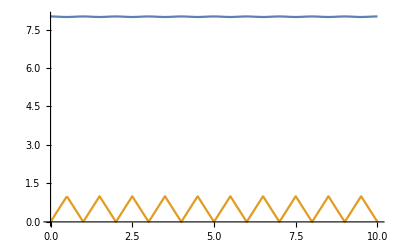

```mathematica
Plot[{xp[t],f[t]},{t,0,10}]
```

```mathematica
f[t_]= 1/2 + Sum[(-1)^((n-1)/2)2/(Pi n) Cos[2 Pi n t/T],{n,1,3,2}]
```

1/2+(2 Cos[2 π t])/π-(2 Cos[6 π t])/(3 π)

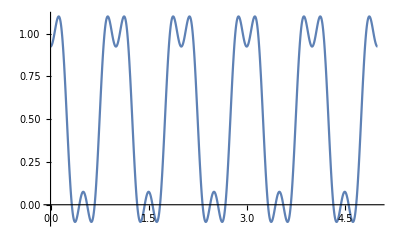

```mathematica
Plot[f[t]/.T->1,{t,0,5}]
```

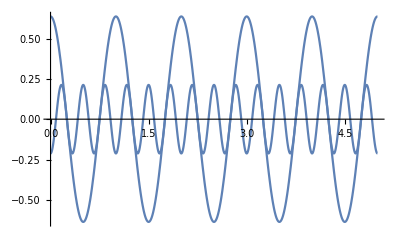

```mathematica
Plot[Table[(-1)^((n-1)/2)2/(Pi n) Cos[2 Pi n t/T],{n,1,3,2}]/.T->1,{t,0,5}]
```

## Periodic Extension of a Function

```mathematica
Clear["Global`*"]
```

```mathematica
f[t_] = Piecewise[{{t^2,0<t<2}}]
```

Piecewise[{{t^2, 0<t<2}, {0, True}}]

```mathematica
T=2;
```

```mathematica
c[n_] = 1/T Integrate[f[t] Exp[I 2 Pi n t/T],{t,0,2}]
```

(-ⅈ+ⅈ ⅇ^(2 ⅈ n π)+2 ⅇ^(2 ⅈ n π) n π-2 ⅈ ⅇ^(2 ⅈ n π) n^2 π^2)/(n^3 π^3)

```mathematica
c[0]= Limit[c[n],n->0]
```

4/3

```mathematica
fPapprox[t_,M_]:= Sum[c[n] Exp[-I n 2Pi t/T],{n,-M,M}]
```

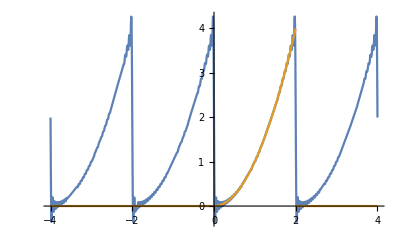

```mathematica
Plot[{fPapprox[t,40],f[t]},{t,-4,4}]
```

## Even Periodic Extension

```mathematica
a[n_]= 2/T Integrate[f[t] Cos[n 2Pi t/(2T)],{t,0,2}]
```

(8 (2 n π Cos[n π]-2 Sin[n π]+n^2 π^2 Sin[n π]))/(n^3 π^3)

```mathematica
a[0]= 1/T Integrate[f[t] Cos[0 2Pi t/(2T)],{t,0,2}]
```

4/3

```mathematica
fPapprox[t_,M_]:= Sum[a[n] Cos[2 Pi n t/(2T)],{n,0,M}]
```

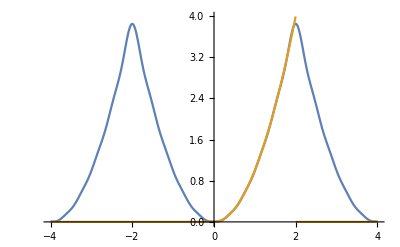

```mathematica
Plot[{fPapprox[t,10],f[t]},{t,-4,4}]
```

## Odd Periodic Extension

```mathematica
f[t_] = Piecewise[{{t(4-t^2),0<t<2}}]
```

Piecewise[{{t (4-t^2), 0<t<2}, {0, True}}]

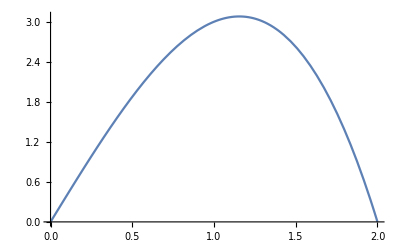

```mathematica
Plot[f[t],{t,0,2}]
```

```mathematica
b[n_] = 2/T Integrate[f[t] Sin[2 Pi n t/(2T)],{t,0,2}]
```

-(32 (3 n π Cos[n π]-3 Sin[n π]+n^2 π^2 Sin[n π]))/(n^4 π^4)

```mathematica
Simplify[b[n],n∈Integers]
```

-(96 (-1)^n)/(n^3 π^3)

```mathematica
fPapprox[t_,M_]:= Sum[b[n] Sin[2 Pi n t/(2T)],{n,1,M}]
```

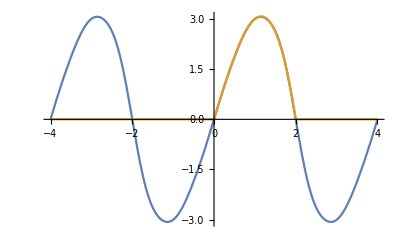

```mathematica
Plot[{fPapprox[t,5],f[t]},{t,-4,4}]
```

```mathematica
Integrate[Exp[I ω t]/(1+t^2),{t,-Infinity,Infinity},Assumptions->ω∈Reals](* Fourier Transform*)
```

ⅇ^(-Abs[ω]) π

## Discretized Green Function (Boundary Value)

```mathematica
(*
```

```mathematica
(* ϕ'' +ϕ(x)=x^3,ϕ(0)=1 , ϕ(1)=0. *)
```

```mathematica
Clear["Global'*"]
```

```mathematica
a = 0; b = 1; M=40;
Δx= (b-a)/M ;
x[n_]  = a + n Δx;
Subscript[u, o][n_] = 1;
Subscript[u, 1][n_] = 0;
```

```mathematica
L = Table[KroneckerDelta[n,m](Subscript[u, o][n]-2/Δx^2) + KroneckerDelta[n+1,m](1/Δx^2+ Subscript[u, 1][n]/(2 Δx)) + KroneckerDelta[n-1,m](1/Δx^2 - Subscript[u, 1][n]/(2Δx)),{n,0,M},{m,0,M}]; (*Do not Change*)
```

```mathematica
L[[1,1]] = 1; L[[1,2]]=0;
L[[M+1,M+1]]= 1;L[[M+1,M]]=0;(* Do not change)
```

```mathematica
ϕa = 1; ϕb = 0;
```

```mathematica
ρ= Table[x[n]^3,{n,0,M}];
```

```mathematica
ρ[[1]]=ϕa ;
ρ[[M+1]]=ϕb;
```

```mathematica
ϕ = Inverse[L].ρ;
```

```mathematica
sol = Table[{x[n],ϕ[[n+1]]},{n,0,M}];
```

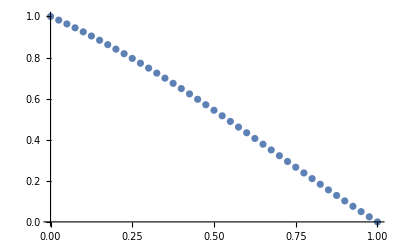

```mathematica
p1 = ListPlot[sol]
```

## Fourier Transform Convention

```mathematica
{{Table 2.1 Fourier Transform Conventions, }, {{{Time:}, {f̃(ω)=∫_(-∞)^∞ f(t)ⅇ^(ⅈ ω t)ⅆt}, {f(t)= ∫_(-∞)^∞ f̃(ω) ⅇ^(-ⅈ ω t)ⅆω/(2 π)}, {}}, {{}, {Fourier transform}, {Inverse Fourier transform}, {}}}, {Space:, }, {f̃(k)=∫_(-∞)^∞ f(x)ⅇ^(-ⅈ k x)ⅆx, Fourier transform}, {f(x)= ∫_(-∞)^∞ f̃(k) ⅇ^(ⅈ k x)ⅆk/(2 π), Inverse Fourier transform}}
```

## Forming Green Function

```mathematica
g(t,Subscript[t, o])=(Subscript[x, 2](Subscript[t, o])Subscript[x, 1](t)-Subscript[x, 1](Subscript[t, o])Subscript[x, 2](t))/(W(Subscript[t, o])),  t> Subscript[t, o],
```

```mathematica
W(t)≡Subscript[x, 1]'(t)Subscript[x, 2](t)-Subscript[x, 2]'(t)Subscript[x, 1](t) .
```